```mathematica
((n+1)^3/9^4)/((n)^3/9^4)
```

(1+n)^3/n^3

```mathematica
Table[(1+n)^3/n^3,{n,1,20}]
```

{8,27/8,64/27,125/64,216/125,343/216,512/343,729/512,1000/729,1331/1000,1728/1331,2197/1728,2744/2197,3375/2744,4096/3375,4913/4096,5832/4913,6859/5832,8000/6859,9261/8000}

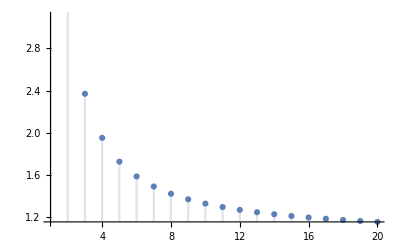

```mathematica
DiscretePlot[(1+n)^3/n^3,{n,1,20}]
```

```mathematica
((n/9)/(81-n))^3
```

n^3/(729 (81-n)^3)

```mathematica
Binomial[n,81]
```

Binomial[n,81]

```mathematica
Table[Binomial[n,81],{n,1,20}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Binomial[81,n]
```

Binomial[81,n]

```mathematica
Table[Binomial[81,n],{n,1,20}]
```

{81,3240,85320,1663740,25621596,324540216,3477216600,32164253550,260887834350,1878392407320,12124169174520,70724320184700,375382930211100,1823288518168200,8144022047817960,33594090947249085,128447994798305325,456703981505085600,1514334254464231200,4694436188839116720}

```mathematica
Table[Multinomial[81,n],{n,1,20}]
```

{82,3403,95284,2024785,34826302,504981379,6348337336,70625252863,706252528630,6426898010533,53752237906276,416579843773639,3012192716517082,20439879147794485,130815226545884704,793067310934426018,4571799792445514692,25144898858450330806,132341572939212267400,668324943343021950370}

```mathematica
Probability[1/9||1/9||1/9||1/9]
```

```mathematica
Expectation[1/9||1/9||1/9||1/9]
```

Expectation[1/9||1/9||1/9||1/9]

WolframAlphaQueryResults

15

WolframAlphaQueryResults

Likelihood is the hypothetical probability that an event that has already occurred would yield a specific outcome. The concept differs from that of a probability in that a probability refers to the occurrence of future events, while a likelihood refers to past events with known outcomes.

```mathematica
81,3240,85320,1663740,25621596,324540216,3477216600,32164253550,260887834350,1878392407320,12124169174520,70724320184700,375382930211100,1823288518168200,8144022047817960,33594090947249085,128447994798305325,456703981505085600,1514334254464231200,4694436188839116720
```

WolframAlphaQueryResults

{{probability,Noun,Amount}→a measure of how likely it is that some event will occur; a number expressing the ratio of favorable cases to the whole number of cases possible,{probability,Noun,Quality}→the quality of being probable; a probable event or the most probable event}

WolframAlphaQueryParseResults

n/9||n/9||n/9

WolframAlphaQueryParseResults

1/729 n^2 Abs[n]

```mathematica
Expectation[x,x\[Distributed]OrderDistribution[{DiscreteUniformDistribution[{1,9}],n}]]
```

Expectation[x,x\[Distributed]OrderDistribution[{DiscreteUniformDistribution[{1,9}],n}]]

```mathematica
Expectation[Probability[x<z<y,z\[Distributed]𝒟],{x,y}\[Distributed]OrderDistribution[{𝒟,n},{k,k+1}]]
```

```mathematica
Probability[{x,y}\[Distributed]{DiscreteUniformDistribution[{1,9}],n}]
```

```mathematica
Probability[x==r∨y==s∨(Floor[x/3]==Floor[r/3]∧Floor[y/3]==Floor[s/3]),{x,y,r,s}\[Distributed]DiscreteUniformDistribution[{1,9}]]
```

Probability[x==r||y==s||(Floor[x/3]==Floor[r/3]&&Floor[y/3]==Floor[s/3]),{x,y,r,s}\[Distributed]DiscreteUniformDistribution[{1,9}]]

```mathematica
n/3-n^2/27+n^3/729
```

n/3-n^2/27+n^3/729

```mathematica
n/3-n^2/27+n^3/729
```

n/3-n^2/27+n^3/729

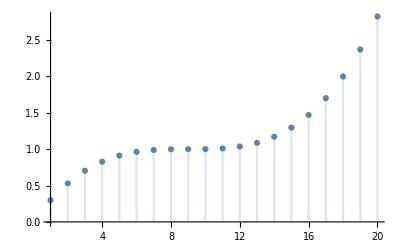

```mathematica
DiscretePlot[n/3-n^2/27+n^3/729,{n,1,20}]
```

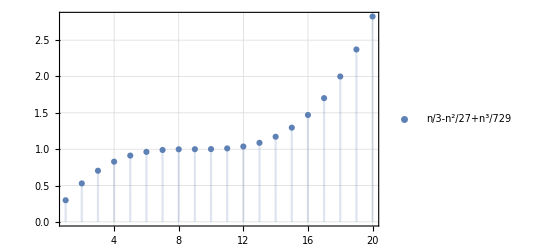

```mathematica
DiscretePlot[n/3-n^2/27+n^3/729,{n,1,20},PlotTheme->"Detailed"]
```

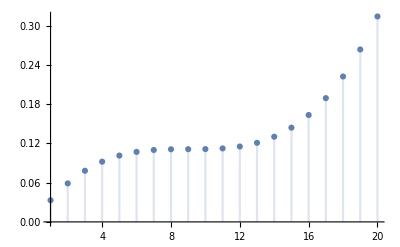

```mathematica
DiscretePlot[1/9(n/3-n^2/27+n^3/729),{n,1,20}]
```

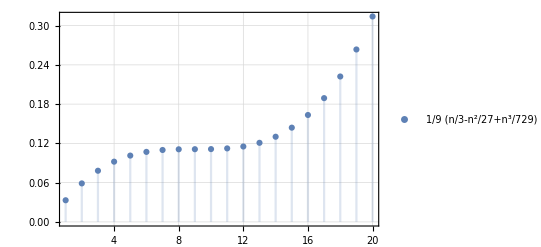

```mathematica
DiscretePlot[1/9 (n/3-n^2/27+n^3/729),{n,1,20},PlotTheme->"Detailed"]
```

```mathematica
1/9 (n/3-n^2/27+n^3/729)
```

1/9 (n/3-n^2/27+n^3/729)

```mathematica
Table[1/9 (n/3-n^2/27+n^3/729),{n,1,80}]
```

{217/6561,386/6561,19/243,604/6561,665/6561,26/243,721/6561,728/6561,1/9,730/6561,737/6561,28/243,793/6561,854/6561,35/243,1072/6561,1241/6561,2/9,1729/6561,2060/6561,91/243,2926/6561,3473/6561,152/243,4825/6561,5642/6561,1,7588/6561,8729/6561,370/243,11377/6561,12896/6561,539/243,16354/6561,18305/6561,28/9,22681/6561,25118/6561,1027/243,30520/6561}

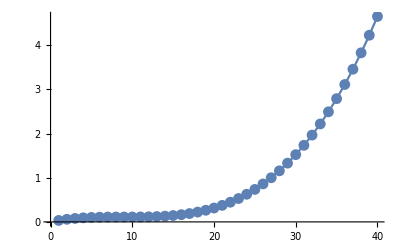

```mathematica
ListLinePlot[%35,Mesh->All]
```

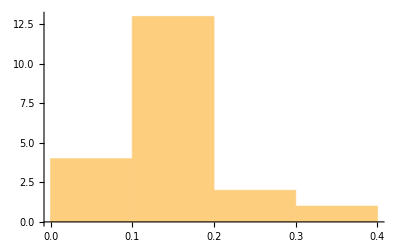

```mathematica
Histogram[{217/6561,386/6561,19/243,604/6561,665/6561,26/243,721/6561,728/6561,1/9,730/6561,737/6561,28/243,793/6561,854/6561,35/243,1072/6561,1241/6561,2/9,1729/6561,2060/6561}]
```

```mathematica
((n+1)/3-(n+1)^2/27+(n+1)^3/729)/(n/3-n^2/27+n^3/729)
```

((1+n)/3-1/27 (1+n)^2+1/729 (1+n)^3)/(n/3-n^2/27+n^3/729)

```mathematica
Simplify[((1+n)/3-1/27 (1+n)^2+1/729 (1+n)^3)/(n/3-n^2/27+n^3/729)]
```

(217+192 n-24 n^2+n^3)/(243 n-27 n^2+n^3)

```mathematica
Table[(217+192 n-24 n^2+n^3)/(243 n-27 n^2+n^3),{n,1,80}]
```

{386/217,513/386,604/513,665/604,702/665,721/702,104/103,729/728,730/729,737/730,756/737,793/756,14/13,135/122,1072/945,1241/1072,1458/1241,1729/1458,2060/1729,2457/2060,418/351,3473/2926,4104/3473,4825/4104,5642/4825,6561/5642,7588/6561,1247/1084,9990/8729,11377/9990,416/367,14553/12896,16354/14553,18305/16354,2916/2615,22681/20412,25118/22681,27729/25118,30520/27729,33497/30520,36666/33497,5719/5238,43604/40033,47385/43604,51382/47385,55601/51382,60048/55601,64729/60048,9950/9247,74817/69650,80236/74817,85913/80236,91854/85913,98065/91854,104552/98065,15903/14936,118378/111321,125729/118378,133380/125729,141337/133380,149606/141337,5103/4826,23872/22599,176345/167104,185922/176345,195841/185922,206108/195841,216729/206108,227710/216729,34151/32530,250776/239057,262873/250776,275354/262873,4725/4514,301492/288225,315161/301492,47034/45023,343729/329238,358640/343729,373977/358640}

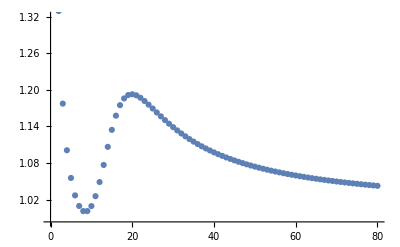

```mathematica
ListPlot[%128]
```

```mathematica
FittedModel[%78,HermiteH,x]
```

FittedModel[%78,HermiteH,x]

```mathematica
Interpolation[%78]
```

InterpolatingFunction[…]

```mathematica
(%98)^(-1)
```

InterpolatingFunction[…][#1]&

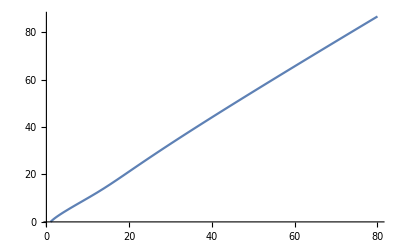

```mathematica
Plot[%117[x],{x,1,80}]
```

```mathematica
%98'
```

InterpolatingFunction[…]

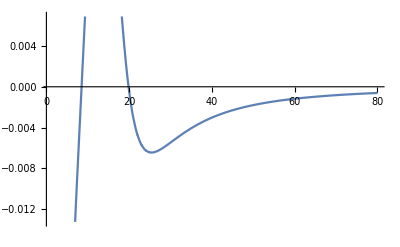

```mathematica
Plot[%107[x],{x,1,80}]
```

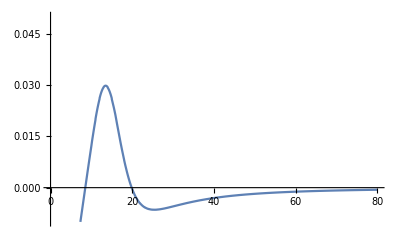

```mathematica
Plot[%107[x],{x,1,80},PlotRange->{-.01,.05}]
```

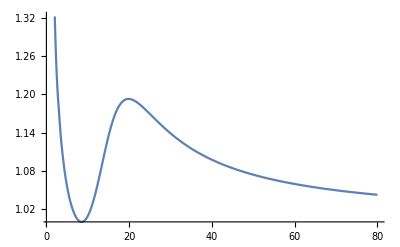

```mathematica
Plot[%98[x],{x,1,80}]
```

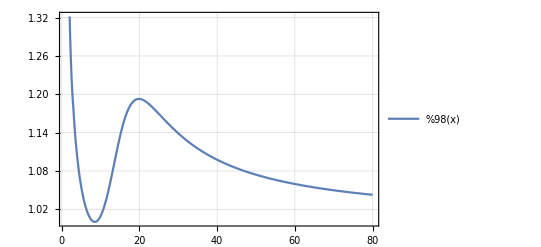

```mathematica
Plot[%98[x],{x,1,80},PlotTheme->"Detailed"]
```

```mathematica
%98[x]
```

InterpolatingFunction[…][x]

```mathematica
Plot[%102,{x,1,80}]
```

-Graphics-

```mathematica
∂_x %102
```

InterpolatingFunction[…][x]

```mathematica
Plot[%103,{x,1,80}]
```

-Graphics-

```mathematica
Plot[%98[x],{x,1,80}]
```

-Graphics-

```mathematica
InterpolatingFunction[%78]
```

InterpolatingFunction[{386/217,513/386,604/513,665/604,702/665,721/702,104/103,729/728,730/729,737/730,756/737,793/756,14/13,135/122,1072/945,1241/1072,1458/1241,1729/1458,2060/1729,2457/2060,418/351,3473/2926,4104/3473,4825/4104,5642/4825,6561/5642,7588/6561,1247/1084,9990/8729,11377/9990,416/367,14553/12896,16354/14553,18305/16354,2916/2615,22681/20412,25118/22681,27729/25118,30520/27729,33497/30520,36666/33497,5719/5238,43604/40033,47385/43604,51382/47385,55601/51382,60048/55601,64729/60048,9950/9247,74817/69650,80236/74817,85913/80236,91854/85913,98065/91854,104552/98065,15903/14936,118378/111321,125729/118378,133380/125729,141337/133380,149606/141337,5103/4826,23872/22599,176345/167104,185922/176345,195841/185922,206108/195841,216729/206108,227710/216729,34151/32530,250776/239057,262873/250776,275354/262873,4725/4514,301492/288225,315161/301492,47034/45023,343729/329238,358640/343729,373977/358640}]

```mathematica
ListPlot[%78]
```

-Graphics-

```mathematica
FindFit[%78,(ⅇ^(a x)+ⅇ^(b x) x+ⅇ^(c x) x^2+ⅇ^(d x) x^3+ⅇ^(e x) x^4+ⅇ^(f x) x^5),{a,b,c,d,e,f},x]
```

{a→1.28382×10^38,b→-155582.,c→7.78971×10^282,d→-1.08642×10^43,e→-1.47185×10^33,f→0.968698}

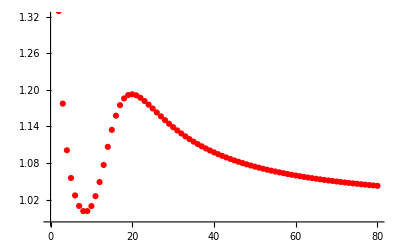

```mathematica
Show[ListPlot[%78,PlotStyle->Red],Plot[ⅇ^(a x)+ⅇ^(b x) x+ⅇ^(c x) x^2+ⅇ^(d x) x^3+ⅇ^(e x) x^4+ⅇ^(f x) x^5/.{a->1.2838222310762284*^38,b->-155582.30949727286,c->7.789709039399845*^282,d->-1.0864203703144787*^43,e->-1.471846525371293*^33,f->0.9686982664765845},{x,1,80}]]
```

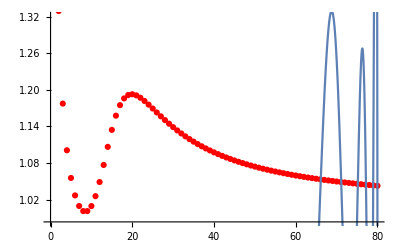

```mathematica
Show[ListPlot[%78,PlotStyle->Red],Plot[ⅇ^(a x) (b+c x+d x^2+e x^3+f x^4+g x^5)/.{a->0.6418963201863782,b->8.057913460112223*^-15,c->-5.248358390324503*^-16,d->1.3670813749588307*^-17,e->-1.78009371359068*^-19,f->1.1586890343538699*^-21,g->-3.016161803944386*^-24},{x,1,80}]]
```

```mathematica
Fourier[%78]
```

{9.84717+0. ⅈ,-0.0110109+0.201692 ⅈ,0.00400831-0.051563 ⅈ,0.139038-0.078857 ⅈ,0.19021-0.00604261 ⅈ,0.167766+0.0504431 ⅈ,0.130091+0.0644905 ⅈ,0.107241+0.0564188 ⅈ,0.0992812+0.0468365 ⅈ,0.096951+0.0425036 ⅈ,0.0943774+0.0415973 ⅈ,0.0905652+0.0411214 ⅈ,0.0865181+0.0398577 ⅈ,0.0830451+0.0379833 ⅈ,0.080273+0.0359808 ⅈ,0.0779908+0.0340995 ⅈ,0.0759955+0.0323534 ⅈ,0.0741965+0.0306811 ⅈ,0.0725745+0.0290427 ⅈ,0.0711249+0.0274324 ⅈ,0.0698343+0.0258578 ⅈ,0.0686828+0.0243242 ⅈ,0.0676511+0.0228311 ⅈ,0.0667243+0.0213754 ⅈ,0.0658909+0.0199536 ⅈ,0.065142+0.0185629 ⅈ,0.0644698+0.0172011 ⅈ,0.0638673+0.015866 ⅈ,0.0633285+0.0145555 ⅈ,0.0628483+0.0132673 ⅈ,0.0624223+0.0119993 ⅈ,0.0620467+0.0107494 ⅈ,0.0617183+0.0095155 ⅈ,0.0614344+0.00829578 ⅈ,0.0611927+0.0070883 ⅈ,0.0609912+0.00589123 ⅈ,0.0608284+0.00470275 ⅈ,0.0607031+0.00352112 ⅈ,0.0606142+0.00234459 ⅈ,0.0605611+0.00117145 ⅈ,0.0605435+9.3095×10^-18 ⅈ,0.0605611-0.00117145 ⅈ,0.0606142-0.00234459 ⅈ,0.0607031-0.00352112 ⅈ,0.0608284-0.00470275 ⅈ,0.0609912-0.00589123 ⅈ,0.0611927-0.0070883 ⅈ,0.0614344-0.00829578 ⅈ,0.0617183-0.0095155 ⅈ,0.0620467-0.0107494 ⅈ,0.0624223-0.0119993 ⅈ,0.0628483-0.0132673 ⅈ,0.0633285-0.0145555 ⅈ,0.0638673-0.015866 ⅈ,0.0644698-0.0172011 ⅈ,0.065142-0.0185629 ⅈ,0.0658909-0.0199536 ⅈ,0.0667243-0.0213754 ⅈ,0.0676511-0.0228311 ⅈ,0.0686828-0.0243242 ⅈ,0.0698343-0.0258578 ⅈ,0.0711249-0.0274324 ⅈ,0.0725745-0.0290427 ⅈ,0.0741965-0.0306811 ⅈ,0.0759955-0.0323534 ⅈ,0.0779908-0.0340995 ⅈ,0.080273-0.0359808 ⅈ,0.0830451-0.0379833 ⅈ,0.0865181-0.0398577 ⅈ,0.0905652-0.0411214 ⅈ,0.0943774-0.0415973 ⅈ,0.096951-0.0425036 ⅈ,0.0992812-0.0468365 ⅈ,0.107241-0.0564188 ⅈ,0.130091-0.0644905 ⅈ,0.167766-0.0504431 ⅈ,0.19021+0.00604261 ⅈ,0.139038+0.078857 ⅈ,0.00400831+0.051563 ⅈ,-0.0110109-0.201692 ⅈ}

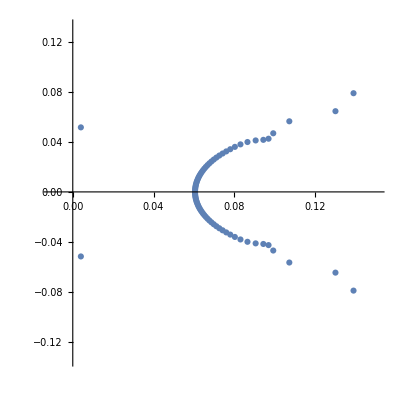

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%91,AspectRatio->1]
```

```mathematica
InterpolatingPolynomial[%78,x]
```

386/217+(-37675/83762+(6405925/42969906+(-964295167/25953823224+(966416239/129769116120+(-12551222707/10121991057360+(184710363763/1042565078908080+(-1293370480261/58383644418852480+(11635573796269/4729075197927050880+(-849481783825237/3452224894486747142400+(2996919072146341/133909986696670139155200+(-8130463480953097/4361639566691541675340800+(4374437580924283/30531476966840791727385600+(-5452638948687487/532120027136368084391577600+(14102491520213077/20584643155012133790937344000+(-(267573793414608463/6257731519123688672444952576000)+(264557524090320463/106381435825102707431564193792000+(-(20057503505128651/147297372680911441059088883712000)+(180189540793554001/24893255983074033538986021347328000+(-(192792775425234001/497865119661480670779720426946560000)+(31023195076199143/1493595358984442012339161280839680000+(-(4539631192425366019/4370260020388477328104385907736903680000)+(4207499086185366019/100515980468934978546400875877948784640000+(-(2090334349345686019/2412383531254439485113621021070770831360000)+(-(2751769580223593981/60309588281360987127840525526769270784000000)+(791243358577199537/120619176562721974255681051053538541568000000+(-(4221671998547598611/9770153301580479914710165135336621867008000000)+(188649337726847889083/10590846178913240227545819006704898103836672000000+(-(1256555618767728769157/4865657699775456523486708111027739765704753152000000)+(-(245734455608156107329433/7893593914481875236948821081659617819901018767360000000)+(137823433756425279243507253/37660336565993026755482825380598036618747760539074560000000+(-(122249677901449371453213422959/485667700355046073038706516108192280235371119911905525760000000)+(1508704377760117932306893960713/112189238782015642871941205220992416734370728699650176450560000000+(-(22091771650627681059576057871/37033340957170212210155349296249923970568978405709766983680000000)+(11671884176377947578766512642503/524986590532053200407594345063075566939626394141363009906278400000000+(-(34586899246914100754050820029651/51298689703417769868399218860449098255243493370384614110842060800000000)+(3626950888983526664048896488883/252724084405701091280483407726965649383754110278209390527696076800000000+(-(6629012239873290333325886928478867/291002179677957389968007985628107320570716275329167541235801979984281600000000)+(-(98506403250557487963563210650001003/5305193583359684724801376353373956536558442865616362097914236096636518400000000)+(2725722478702686968217345443813359948757/2104888606133788511412194081964650995444927791361947825968452313701505040384000000000+(-(2785525035267553397763067679647292946659/44316438491303277037570248374336841228421587823539388011606063577661416931328000000000)+(2432011208638890991886869752522759769365593/954310186471724767727037728492969539012830472192097181441924973081360952199217152000000000+(-(609546814233382547662873589339113450826957/6680171305302073374089264099450786773089813305344680270093474811569526665394520064000000000)+(860120143425401373568905880123397301769514387/291282189596391607403788271792452106453808219366249438497155875683677640717862652870656000000000+(-(14860134003203341842778085366266645819003687031/170400080913889090331216138998584482275477808329255921520836187274951419819949651929333760000000000)+(20602092332568859939351318596654023015027118413627/8755496957517449239398547654025267868278600747573827759583604974561553853188653015433027256320000000000+(-(307920934994705475128777426985276229629912539377151/5349608641043161485272512616609438667518225056767608761105582639457109404298266992429579653611520000000000)+(44536808806570986581965831227897376900993682973423989/35692588853039973429738204178018174789681597578753485654096447370457833945478037373490155448896061440000000000+(-(1063115405111497454104803599906211567057265603426389581/47149909874865804900684167719162008897169390401533354549061406976374798641976487370380495347991697162240000000000)+(23933578820273020575262759525443996312086516669539478009/88756519534713603008990602206476592423995893012616166063300729619040668254423306631000040567233019117568000000000000+(2539951682731381756121518042843329377942350618000389901459/1436832580789828669847807285119488251282372672037552261785057985102849883282303951414190709353163118589509632000000000000+(-(44117111133933412271387595172224607653777972705921033133928731/168494483084061628455712664711392148251381278504499678635010179797041000112749219774439316104426732590754615525376000000000000)+(166594272881165107538145001912667567337249257070064394710098472951/14475866525200986685515642163349833632720919780157080890569629576903183442686623718481404964479613877069501283631628288000000000000+(-(302772129187058611347953737651081918242656773814678282710098472951/781696792360853281017844676820891016166929668128482368090759997152771905905077680797995868081899149361753069316107927552000000000000)+(870718046995006948546536613665215195053981594452722237336105577271633/76657095942867077003014938232440677500409957905019623426820379120786576952581442767455464803451440082160314742484123915386880000000000000+(-(347591923959565734032455394129262733243561225170154156694758444680876973/1144950385002662662117031117439733959146123131269373095502989182548068313363756429174714822304350709067146460993742874800218439680000000000000)+(181589966034438519382533153607237920411555594405227122397538374356112569/24043958085055915904457653466234413142068585756656835005562772833509434580638885012669011268391364890410075680868600370804587233280000000000000+(-(38728334769197827001669526250397248941205410445600359922182484773909673333/218944282322519170225991392463530566071676541900117139560654609421936911291297686925364016609971768692074149149989474976546571346247680000000000000)+(108087542225154361193253008842548822413693300359858412602933611693201513872623/27527645672128012753343671783047234541625819936559827839821543388010705919743566879439092444355140505885790698479026699326223868792374558720000000000000+(-(33831865336007991093402946527231020008353381966632011518481918901020773926537881/407959708860937149004553215824760015906894651459816648586155273010318661730599661153287350025343182297227418151459175684014637735502990960230400000000000000)+(32210982453435535603529833609978552622972194216883571235957146622473714683100793/19290666233281456617215302062570795037883161376171330097431056480916496718975498263105444694055513334340325058304712450201263584350212858262323200000000000000+(-(1099729864591200654880763984045336938486831368553680579682950341337184914621825967/34298804562774429865408807067250873577356260926832624913232418423069531166338435911801480666030702708457097953665778736457846652974678461990410649600000000000000)+(801625455266576739848523213937911887969069777710167679162203619622137394964828673/1367052353287723704635579595966141961154628114083757478684549248576628456486917659913230443688938007951361475581821752495962745168562184413617795891200000000000000+(-(16276044981186308764788778285157171661375693935953572597042159721249536367772173656421/1599079415106542473575967249630283303937480834630965468026720423439042451149529220494983220435374078164930156109373194903597509980531906849772317152221593600000000000000)+(3612364448077784155600119381588500792876922060064178390562444204268436883643531317682321/21691512265920248654057995741234793017911927521769046573782462543950610849843363876014447385205849370307277567623647388867300222885915316417161482169885917184000000000000000+(-(1135943314568294541337480084811109387295187702540095097383338896675722545540425302434566473/448103260389380496695530076022428354164024598744704964121198111232931718936064210950706454083582436291807739991969307759220688004377238606545721898665503277187072000000000000000)+(579566699266133480601724301142753517581740213906732007619405473437124220042085614777297903/16579820634407078377734612812829849104068910153554083672484330115618473600634375805176138801092550142796886379702864387091165456161957828442191710250623621255921664000000000000000+(-(199757794086453456629076494665481765233944602307014254483906022390916468178319071198569991999/488176238759482015754017939660962077020204990561246439652628615924270336697078561207606230859369046404511522563971139013512275691232686300651892716619361904259357474816000000000000000)+(37632569911193343837272284059302065216129005732432385388944428760258614464916491848300927207651/11755772005567086421372506004975627776723556377705375513274949700072353978002348832440365645324466006467041974862988998584389110920574318805998228508910854016469587351044096000000000000000+(5955193963783991388521934635346245155555850322014622067533141760869129832963111111068154827644471/382415263341097321287247620341857171576817288966755865446834113743353674904416407519285094442404879190372875442293032123950177778246282590759122373394870081155755676529464442880000000000000000+(-(280911944821504475570631337102150942557053920737886887040724462015590733830480842097477083793511297/190060385880525368679762067309903014273678192616477665127076554530446776427494954537084691937875224957615319094819636965603238355788402447607283819577250430334410571235143828111360000000000000000)+(26334269800681047385016415554521339493337342383839951409904657194068530662399920144911514603120985771/588426954686106541432543360391459732191307684340614851233429012826263219819524379246814206239661696468777027917561596045507625949520893977792150705411167332315335128544005291832770560000000000000000+(-(2237740426748030250967910122361185264316338698380131105833383823289680158494346393817018686107379037827/2118925463824669655698588640769646495620898971310554079291577875187373854570107289667777956669021768984066077531139307359872961044224739214029534690185613563667521797886963055889806786560000000000000000)+(5695053910409137133134963207595807325492595607864129921450172529256728780825378021607586482501354629931/258508906586609697995227814173896872465749674499887597673572500772859610257553089339468910713620655816056061458798995497904501247395418184111603232202644854767437659342209492818556427960320000000000000000+(-(8231698726493667309220325617547869517882240011738025590557143709553588393205776092924066482501354629931/19388167993995727349642086063042265434931225587491569825517937557964470769316481700460168303521549186204204609409924662342837593554656363808370242415198364107557824450665711961391732097024000000000000000000)+(2374406386292646029512012313411299540982796449953908199724317132541347803559338805651402722951730200891383/307651449728724201584120621648354667921488687622316229991318633169780222167513931622901950640279942486688318742116684542056146934525287180911219006644367641658727558383163517403364004915576832000000000000000000+(-(1854100697031398370591326074089950775471678631654430742469489882679093083373092036345410859577347387464061517/13851391221136349727921862748473872213829185182819543622899138821203014942647979743457914523677323850578168174726319488136993903433132004746165813336149364330400890861085171044051657593314015707136000000000000000000)+(86947993483026524190949245670588853942189522076108197102269550772639190922742225400493095243521224978511142421/38977814896277688134372121774205476409715327104454195754838176642865284048611414998090571469627989315526965243679863039617500844260833461355710598727924311225748106883093671317961364467585640199880704000000000000000000+(-(6085799781892573080148955179942739274292525415606817693159341497628751471646319794648516521344213289639265578149/169592472613704221072653101839568027858671388231480205729300906573106850895508266656692076464351381511857825775251084085375746173378886390358696815065198678143230013048340563904449896798465120509680943104000000000000000000)+(34001188084077082449175042758352611152411306521840634691988317684090527547897769876010299571964988177452827586841967 (-79+x))/60822644378178881845496308443742677511233906675338060982756477133379041005165084753756046303174979465412690636036048796379157607620603815038243025754982853929288011879656859838691910987801530819591973434818560000000000000000000) (-78+x)) (-77+x)) (-76+x)) (-75+x)) (-74+x)) (-73+x)) (-72+x)) (-71+x)) (-70+x)) (-69+x)) (-68+x)) (-67+x)) (-66+x)) (-65+x)) (-64+x)) (-63+x)) (-62+x)) (-61+x)) (-60+x)) (-59+x)) (-58+x)) (-57+x)) (-56+x)) (-55+x)) (-54+x)) (-53+x)) (-52+x)) (-51+x)) (-50+x)) (-49+x)) (-48+x)) (-47+x)) (-46+x)) (-45+x)) (-44+x)) (-43+x)) (-42+x)) (-41+x)) (-40+x)) (-39+x)) (-38+x)) (-37+x)) (-36+x)) (-35+x)) (-34+x)) (-33+x)) (-32+x)) (-31+x)) (-30+x)) (-29+x)) (-28+x)) (-27+x)) (-26+x)) (-25+x)) (-24+x)) (-23+x)) (-22+x)) (-21+x)) (-20+x)) (-19+x)) (-18+x)) (-17+x)) (-16+x)) (-15+x)) (-14+x)) (-13+x)) (-12+x)) (-11+x)) (-10+x)) (-9+x)) (-8+x)) (-7+x)) (-6+x)) (-5+x)) (-4+x)) (-3+x)) (-2+x)) (-1+x)

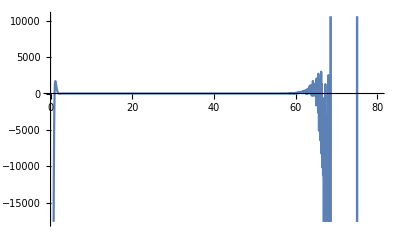

```mathematica
Plot[%88,{x,0,80}]
```

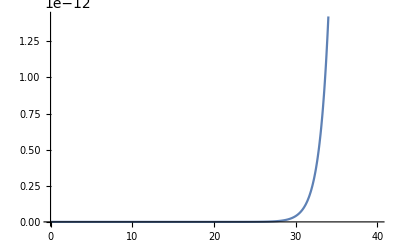

```mathematica
Plot[4.3716574551572235*^-26 ⅇ^x-2.816486099114602*^-27 ⅇ^x x+7.257427321381146*^-29 ⅇ^x x^2-9.349336426566368*^-31 ⅇ^x x^3+6.021453515162623*^-33 ⅇ^x x^4-1.5510786777614568*^-35 ⅇ^x x^5,{x,0,40}]
```

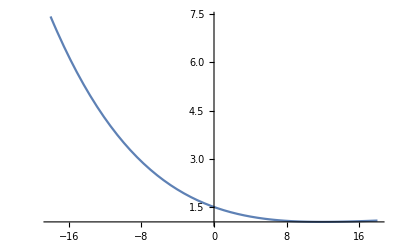

```mathematica
Plot[1.5122697252250534+3.641186793513754*^-36 ⅇ^x-0.10056756698184728 x+0.007500484223959509 x^2-0.0002276116504693695 x^3+2.994736792536534*^-6 x^4-1.4260714066120725*^-8 x^5,{x,-18.,18.}]
```

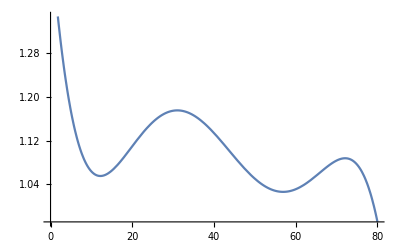

```mathematica
Plot[1.4938163167728402-0.0932687932078648 x+0.006792458999632212 x^2-0.0002013607200014415 x^3+2.5859762900645325*^-6 x^4-1.2011051055702606*^-8 x^5,{x,0,80}]
```

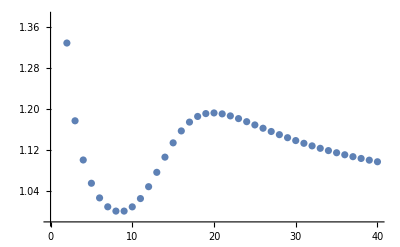

```mathematica
ListPlot[%45]
```

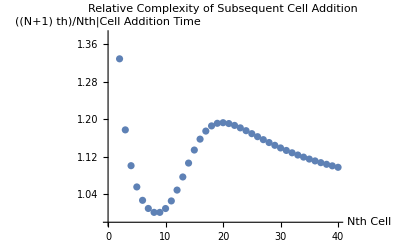

```mathematica
Show[%46,AxesLabel->{HoldForm[Nth Cell],HoldForm[((N+1) th)/Nth|Cell Addition Time]},PlotLabel->HoldForm[Relative Complexity of Subsequent Cell Addition],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
32!!!!
```

SystemException[MemoryAllocationFailure]

```mathematica
Fac
```

```mathematica
QFactorial[8,2]
```

19923090075

```mathematica
Factorial2[8]
```

384

```mathematica
32+28+24+20 +16+12+8 +4+1
```

```mathematica
33*81
```

2673

```mathematica
729/32
```

729/32

```mathematica
N[729/32]
```

22.7813

```mathematica
729-33
```

696

```mathematica
%/22.09090909090909
```

31.5062

```mathematica
%%-%/22.09090909090909
```

694.574

```mathematica
N[243/11]
```

22.0909

```mathematica
%%
```

31.5062

```mathematica
696-31.506172839506174
```

```mathematica
%/22.09090909090909
```

30.08

```mathematica
(%%-%)/22.09090909090909
```

28.7183

```mathematica
Table[1/9 (n/3-n^2/27+n^3/729),{n,1,80}]
```

{217/6561,386/6561,19/243,604/6561,665/6561,26/243,721/6561,728/6561,1/9,730/6561,737/6561,28/243,793/6561,854/6561,35/243,1072/6561,1241/6561,2/9,1729/6561,2060/6561,91/243,2926/6561,3473/6561,152/243,4825/6561,5642/6561,1,7588/6561,8729/6561,370/243,11377/6561,12896/6561,539/243,16354/6561,18305/6561,28/9,22681/6561,25118/6561,1027/243,30520/6561,33497/6561,1358/243,40033/6561,43604/6561,65/9,51382/6561,55601/6561,2224/243,64729/6561,69650/6561,2771/243,80236/6561,85913/6561,14,98065/6561,104552/6561,4123/243,118378/6561,125729/6561,4940/243,141337/6561,149606/6561,217/9,167104/6561,176345/6561,6886/243,195841/6561,206108/6561,8027/243,227710/6561,239057/6561,344/9,262873/6561,275354/6561,10675/243,301492/6561,315161/6561,12194/243,343729/6561,358640/6561}

```mathematica
Interpolation[%119]
```

InterpolatingFunction[…]

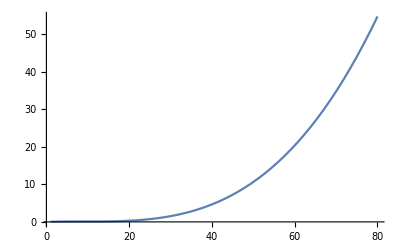

```mathematica
Plot[%121[x],{x,1,80}]
```

```mathematica
(%121)^(-1)
```

InterpolatingFunction[…][#1]&

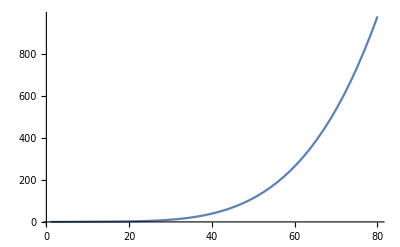

```mathematica
Plot[%125[x],{x,1,80}]
```

```mathematica
%121'
```

InterpolatingFunction[…]

```mathematica
%123[60]
```

289/243

```mathematica
N[289/243]
```

1.1893

```mathematica
%123[61]
```

2704/2187

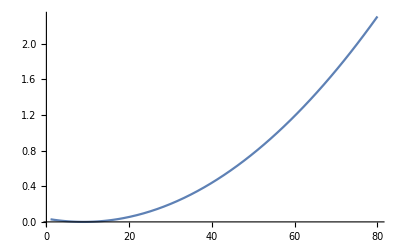

```mathematica
Plot[%123[x],{x,1,80}]
```

```mathematica
Plot[%121[x],{x,1,80}]
```

-Graphics-

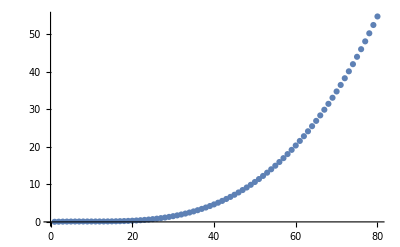

```mathematica
ListPlot[%119]
```

```mathematica
Table[(217+192 n-24 n^2+n^3)/(243 n-27 n^2+n^3),{n,1,80}]
```

{386/217,513/386,604/513,665/604,702/665,721/702,104/103,729/728,730/729,737/730,756/737,793/756,14/13,135/122,1072/945,1241/1072,1458/1241,1729/1458,2060/1729,2457/2060,418/351,3473/2926,4104/3473,4825/4104,5642/4825,6561/5642,7588/6561,1247/1084,9990/8729,11377/9990,416/367,14553/12896,16354/14553,18305/16354,2916/2615,22681/20412,25118/22681,27729/25118,30520/27729,33497/30520,36666/33497,5719/5238,43604/40033,47385/43604,51382/47385,55601/51382,60048/55601,64729/60048,9950/9247,74817/69650,80236/74817,85913/80236,91854/85913,98065/91854,104552/98065,15903/14936,118378/111321,125729/118378,133380/125729,141337/133380,149606/141337,5103/4826,23872/22599,176345/167104,185922/176345,195841/185922,206108/195841,216729/206108,227710/216729,34151/32530,250776/239057,262873/250776,275354/262873,4725/4514,301492/288225,315161/301492,47034/45023,343729/329238,358640/343729,373977/358640}

```mathematica
Table[(243 n-27 n^2+n^3)/(217+192 n-24 n^2+n^3),{n,0,80}]
```

{0,217/386,386/513,513/604,604/665,665/702,702/721,103/104,728/729,729/730,730/737,737/756,756/793,13/14,122/135,945/1072,1072/1241,1241/1458,1458/1729,1729/2060,2060/2457,351/418,2926/3473,3473/4104,4104/4825,4825/5642,5642/6561,6561/7588,1084/1247,8729/9990,9990/11377,367/416,12896/14553,14553/16354,16354/18305,2615/2916,20412/22681,22681/25118,25118/27729,27729/30520,30520/33497,33497/36666,5238/5719,40033/43604,43604/47385,47385/51382,51382/55601,55601/60048,60048/64729,9247/9950,69650/74817,74817/80236,80236/85913,85913/91854,91854/98065,98065/104552,14936/15903,111321/118378,118378/125729,125729/133380,133380/141337,141337/149606,4826/5103,22599/23872,167104/176345,176345/185922,185922/195841,195841/206108,206108/216729,216729/227710,32530/34151,239057/250776,250776/262873,262873/275354,4514/4725,288225/301492,301492/315161,45023/47034,329238/343729,343729/358640,358640/373977}

```mathematica
Interpolation[%130]
```

InterpolatingFunction[…]

```mathematica
%132[61]
```

133380/141337

```mathematica
N[133380/141337]
```

0.943702

```mathematica
(%132)^(-1)
```

InterpolatingFunction[…][#1]&

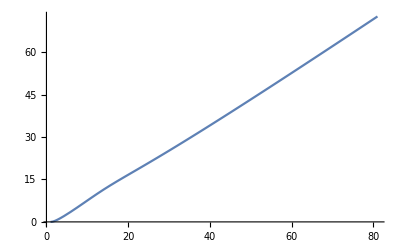

```mathematica
Plot[%136[x],{x,1,81}]
```

```mathematica
%132'
```

InterpolatingFunction[…]

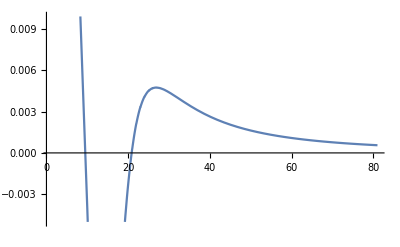

```mathematica
Plot[%134[x],{x,1,81}]
```

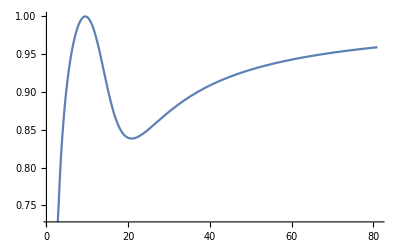

```mathematica
Plot[%132[x],{x,1,81}]
```

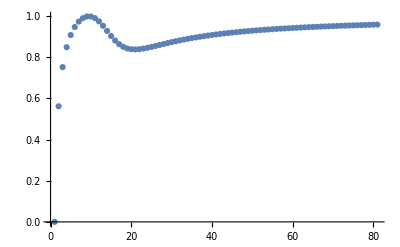

```mathematica
ListPlot[%130]
```

```mathematica
Table[(n/3-n^2/27+n^3/729),{n,1,80}]
```

{217/729,386/729,19/27,604/729,665/729,26/27,721/729,728/729,1,730/729,737/729,28/27,793/729,854/729,35/27,1072/729,1241/729,2,1729/729,2060/729,91/27,2926/729,3473/729,152/27,4825/729,5642/729,9,7588/729,8729/729,370/27,11377/729,12896/729,539/27,16354/729,18305/729,28,22681/729,25118/729,1027/27,30520/729,33497/729,1358/27,40033/729,43604/729,65,51382/729,55601/729,2224/27,64729/729,69650/729,2771/27,80236/729,85913/729,126,98065/729,104552/729,4123/27,118378/729,125729/729,4940/27,141337/729,149606/729,217,167104/729,176345/729,6886/27,195841/729,206108/729,8027/27,227710/729,239057/729,344,262873/729,275354/729,10675/27,301492/729,315161/729,12194/27,343729/729,358640/729}

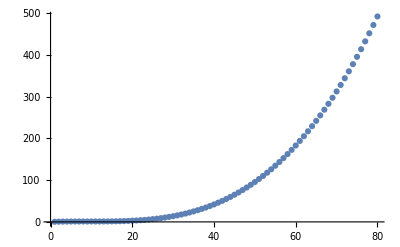

```mathematica
ListPlot[%139]
```

```mathematica
%132[62]
```

141337/149606

```mathematica
(8/9)^3
```

512/729

```mathematica
N[512/729]
```

0.702332

```mathematica
Table[N[((60-n)/(81-n))^(n+1)],{n,0,60}]
```

{0.740741,0.543906,0.395733,0.285181,0.203463,0.143646,0.100306,0.0692394,0.0472198,0.0317963,0.0211265,0.0138413,0.00893507,0.00567865,0.00355014,0.00218121,0.00131574,0.000778382,0.000451093,0.000255766,0.000141688,0.0000765762,0.0000403113,0.0000206333,0.0000102492,4.93038×10^-6,2.2916×10^-6,1.02651×10^-6,4.41926×10^-7,1.82285×10^-7,7.17932×10^-8,2.68965×10^-8,9.54431×10^-9,3.19276×10^-9,1.00148×10^-9,2.92791×10^-10,7.92415×10^-11,1.96995×10^-11,4.45877×10^-12,9.09495×10^-13,1.65231×10^-13,2.63713×10^-14,3.63864×10^-15,4.25867×10^-16,4.13354×10^-17,3.23805×10^-18,1.9807×10^-19,9.08433×10^-21,2.9696×10^-22,6.48837×10^-24,8.72075×10^-26,6.46108×10^-28,2.2734×10^-30,3.08149×10^-33,1.18389×10^-36,8.01332×10^-41,4.31359×10^-46,4.17619×10^-53,2.62318×10^-63,2.84865×10^-81,0.}

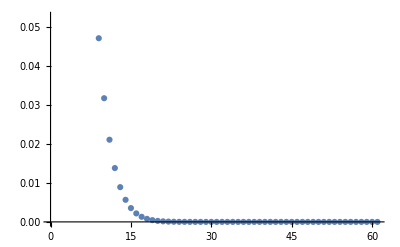

```mathematica
ListPlot[%157]
```

```mathematica
ListPlot[%155]
```

-Graphics-

```mathematica
(60!21!)/(81!)
```

1/13636219405675529520

```mathematica
N[1/13636219405675529520]
```

7.33341×10^-20

```mathematica
Table[N[(60!(21+n)!)/(81!n!)],{n,59,0,-1}]
```

{0.740741,0.546296,0.401078,0.293096,0.21316,0.154261,0.111068,0.0795486,0.0566647,0.0401375,0.0282659,0.0197861,0.0137642,0.00951352,0.00653167,0.00445341,0.00301462,0.00202545,0.0013503,0.000892939,0.000585534,0.000380597,0.00024513,0.000156376,0.0000987639,0.0000617274,0.0000381588,0.0000233193,0.0000140795,8.39358×10^-6,4.9374×10^-6,2.86369×10^-6,1.63639×10^-6,9.20472×10^-7,5.09197×10^-7,2.76738×10^-7,1.47593×10^-7,7.71511×10^-8,3.94727×10^-8,1.97363×10^-8,9.62748×10^-9,4.57305×10^-9,2.11064×10^-9,9.44233×10^-10,4.08317×10^-10,1.70132×10^-10,6.80529×10^-11,2.60202×10^-11,9.4619×10^-12,3.25253×10^-12,1.0492×10^-12,3.14761×10^-13,8.68305×10^-14,2.17076×10^-14,4.82392×10^-15,9.27676×10^-16,1.48428×10^-16,1.85535×10^-17,1.61335×10^-18,7.33341×10^-20}

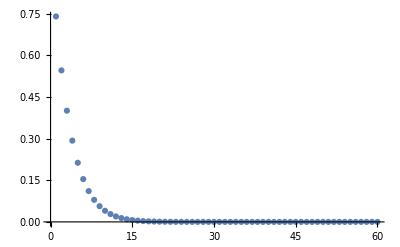

```mathematica
ListPlot[%164,PlotRange->All]
```

```mathematica
Table[(60!(21+n)!)/(81!n!),{n,59,0,-1}]
```

{20/27,59/108,1711/4266,32509/110916,65018/305019,8555/55458,1711/15405,90683/1139970,181366/3200685,1541611/38408220,7708055/272698362,10791277/545396724,43165108/3136031163,29834707/3136031163,59669414/9135395127,149173535/33496448799,119338828/39586712217,1282892401/633387395472,1282892401/950081093208,52598588441/58905027778896,262992942205/449150836814082,52598588441/138200257481256,16938528481/69100128740628,584087189/3735142094088,30741431/311261841174,153707155/2490094729392,522604327/13695521011656,522604327/22410852564528,19720918/1400678285283,9860459/1174762432818,2900135/587381216409,16820783/5873812164090,4805938/2936906082045,2402969/2610583184040,51127/100407045540,255635/923744818968,51127/346404307113,51127/662686500564,1189/30122113662,1189/60244227324,145/15061056831,551/120488454648,551/261058318404,493/522116636808,986/2414789445237,2465/14488736671422,493/7244368335711,29/1114518205494,58/6129850130217,29/8916145643952,145/138200257481256,29/92133504987504,1/11516688123438,1/46066752493752,1/207300386221884,5/5389810041768984,1/6737262552211230,1/53898100417689840,1/619828154803433160,1/13636219405675529520}